```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree,colofun}

```mathematica
repChromEmbed=Table[allGraphs5[k,"colofour"]->ChromaticPolynomial[EmbedGraphInPlantri8[ allGraphs5,k],x],{k,allGraphs5AtomKeys}];Length[repChromEmbed]
```

52

```mathematica
Table[allGraphs5[k,"chromembed"]=Simplify[(allGraphs5[k,"colofour"]/.repChromEmbed)],{k,Keys[allGraphs5]}];
```

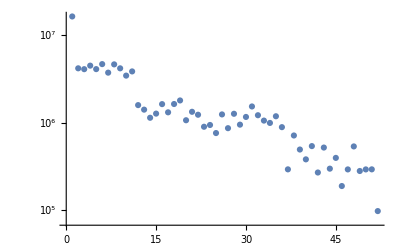

```mathematica
ConversionMatrix["E","C"].Table[(allGraphs5[k,"chromembed"]/.x->5),{k,allGraphs5AtomKeys}]//ListLogPlot
```

```mathematica
CoefficientList[CharacteristicPolynomial[ConversionMatrix["T","E"],x],x]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

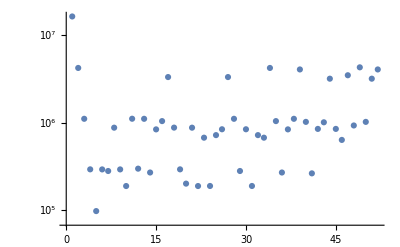

```mathematica
Table[(allGraphs5[k,"chromembed"]/.x->5),{k,allGraphs5NullAtomKeys}]//ListLogPlot
```

```mathematica
Table[VertexCount[EmbedGraphInPlantri8[ allGraphs5,k]], {k,allGraphs5AtomKeys}]
```

{16,15,15,15,14,15,14,15,14,14,15,14,14,14,13,15,14,14,14,13,15,14,14,14,13,14,13,15,14,14,14,13,14,13,14,13,13,15,14,14,14,13,14,13,14,13,13,14,13,13,13,12}

## Barely four colorable

```mathematica
SymbolRank[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
count=10
```

10

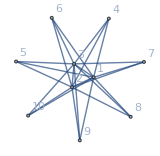
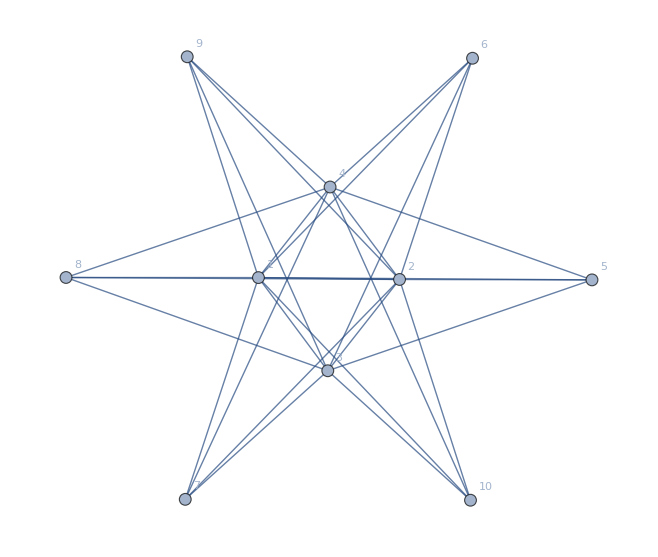
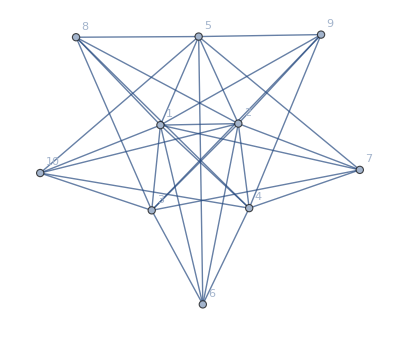
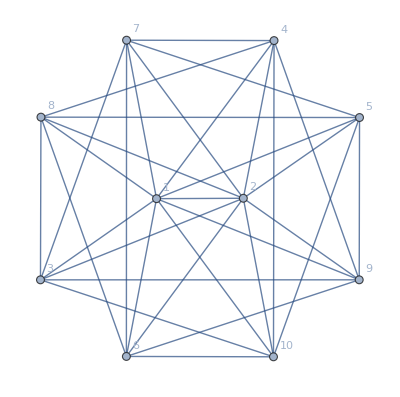
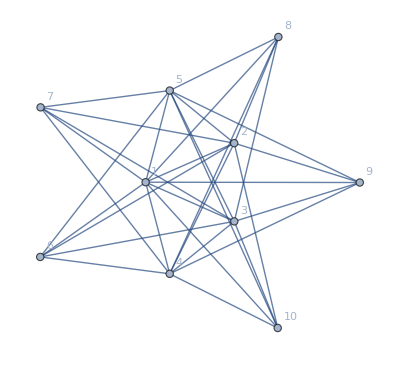
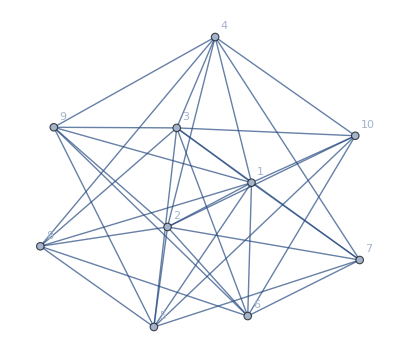
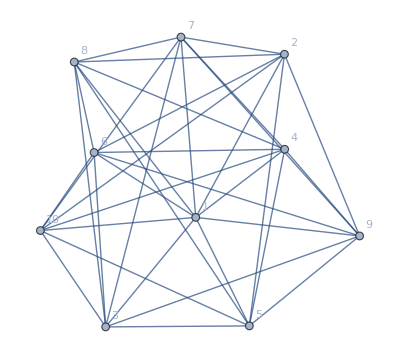
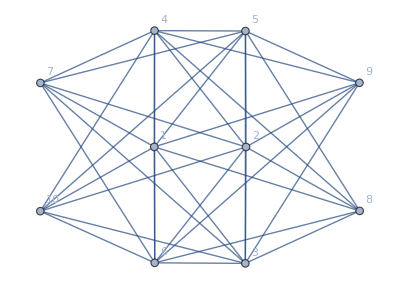

```mathematica
graphs=Map[First,Tally[Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
g
],{part,KSetPartitions[count,4]}],IsomorphicGraphQ[#1,#2]&]]
```

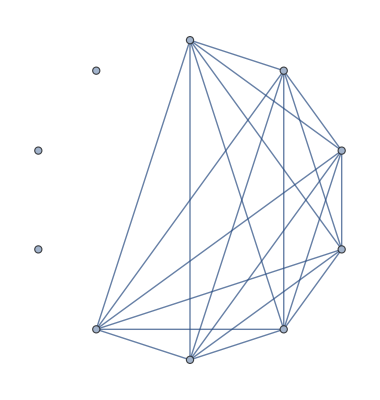
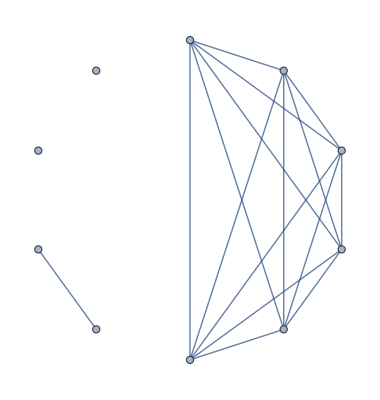
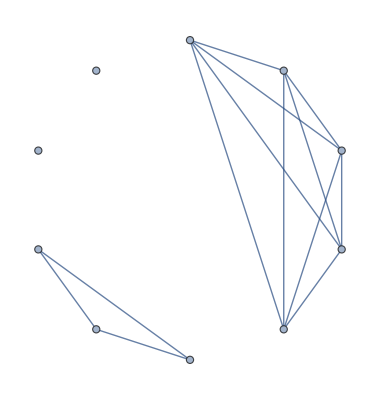
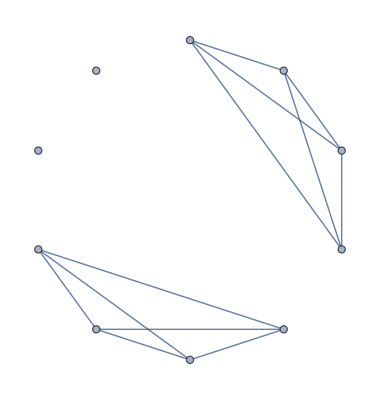
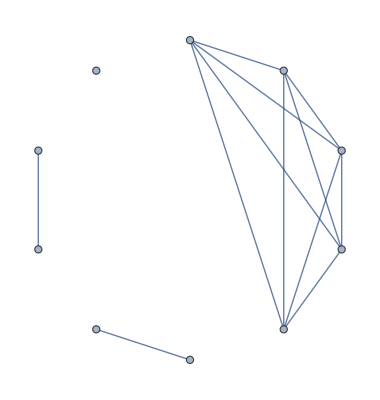
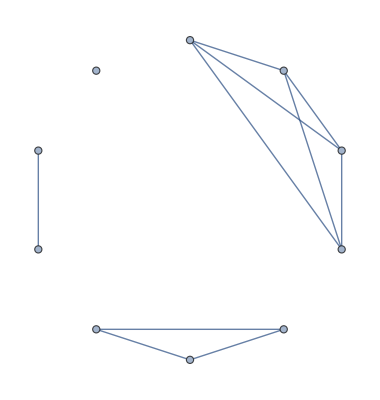
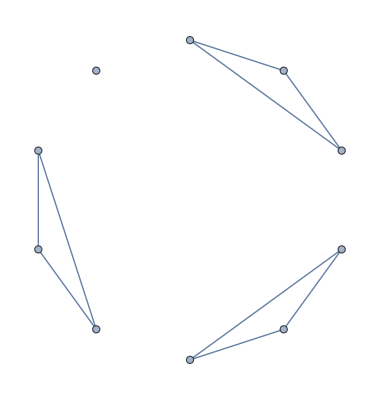
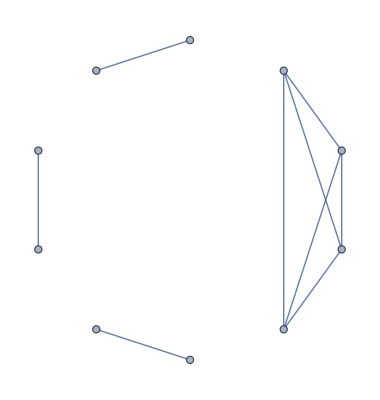

```mathematica
Map[GraphComplement,graphs]
```

```mathematica
EdgeCount[CompleteGraph[7]]
```

21

```mathematica
TriangleNumber[7-1]
```

21

```mathematica
TriangleNumber[count-1]-TriangleNumber[7-1]
```

24

```mathematica
IntegerPartitions[count,{4}]
```

{{7,1,1,1},{6,2,1,1},{5,3,1,1},{5,2,2,1},{4,4,1,1},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}

```mathematica
Length[IntegerPartitions[count,{4}]]
```

9

```mathematica
Map[EdgeCount[#]&,graphs]
```

{24,29,32,33,33,35,36,36,37}

```mathematica
EdgeCount[CompleteGraph[count]]
```

45

```mathematica
fors=Map[FindFullFormula[#]&,graphs];
```

```mathematica
Map[Sort[Tally[#]]&,Map[Map[SymbolRank,#]&,fors]]
```

{{{4,1},{5,63},{6,301},{7,350},{8,140},{9,21},{10,1}},{{4,1},{5,32},{6,121},{7,155},{8,80},{9,16},{10,1}},{{4,1},{5,18},{6,71},{7,100},{8,56},{9,13},{10,1}},{{4,1},{5,14},{6,61},{7,86},{8,50},{9,12},{10,1}},{{4,1},{5,17},{6,56},{7,75},{8,46},{9,12},{10,1}},{{4,1},{5,11},{6,38},{7,54},{8,35},{9,10},{10,1}},{{4,1},{5,9},{6,30},{7,45},{8,30},{9,9},{10,1}},{{4,1},{5,10},{6,30},{7,41},{8,28},{9,9},{10,1}},{{4,1},{5,8},{6,24},{7,34},{8,24},{9,8},{10,1}}}

```mathematica
Map[With[{g=#},Table[VertexDegree[g,v],{v,VertexList[g]}]]&,Table[MinimalGraph[k],{k,3,14}]]
```

{{3,3,3,3},{4,4,3,4,3},{5,5,3,4,4,3},{6,6,3,4,4,4,3},{7,7,3,4,4,4,4,3},{8,8,3,4,4,4,4,4,3},{9,9,3,4,4,4,4,4,4,3},{10,10,3,4,4,4,4,4,4,4,3},{11,11,3,4,4,4,4,4,4,4,4,3},{12,12,3,4,4,4,4,4,4,4,4,4,3},{13,13,3,4,4,4,4,4,4,4,4,4,4,3},{14,14,3,4,4,4,4,4,4,4,4,4,4,4,3}}

```mathematica
Map[With[{g=GraphComplement[#]},Table[VertexDegree[g,v],{v,VertexList[g]}]]&,Table[MinimalGraph[k],{k,3,14}]]
```

{{0,0,0,0},{0,0,1,0,1},{0,0,2,1,1,2},{0,0,3,2,2,2,3},{0,0,4,3,3,3,3,4},{0,0,5,4,4,4,4,4,5},{0,0,6,5,5,5,5,5,5,6},{0,0,7,6,6,6,6,6,6,6,7},{0,0,8,7,7,7,7,7,7,7,7,8},{0,0,9,8,8,8,8,8,8,8,8,8,9},{0,0,10,9,9,9,9,9,9,9,9,9,9,10},{0,0,11,10,10,10,10,10,10,10,10,10,10,10,11}}

## Minimal graphs

```mathematica
SymbolRank[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
count=10
```

10

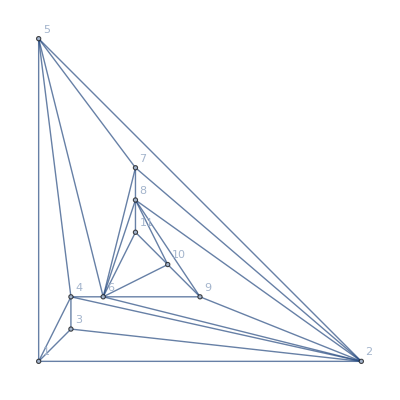

```mathematica
graphs=MinimalGraph2[count]
```

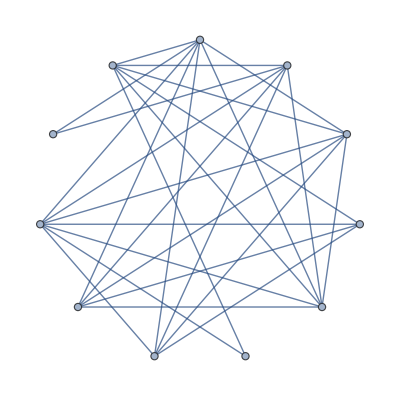

```mathematica
GraphComplement[graphs,GraphLayout->Automatic]
```